```mathematica
X = {{0,1},{1,0}}
MatrixForm[X]
```

{{0,1},{1,0}}

```mathematica
({{0, 1}, {1, 0}})
```

```mathematica
Y={{0,-ⅈ},{ⅈ,0}}
MatrixForm[Y]
```

{{0,-ⅈ},{ⅈ,0}}

(0 | -ⅈ
ⅈ | 0)

```mathematica
({{0, -ⅈ}, {ⅈ, 0}})


Clear[θ]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
M1 = MatrixExp[-ⅈ*(π+ϵ)/2*(X*Cos[ArcCos[-1/(4)]]+Y*Sin[ArcCos[-1/4]])]
MatrixForm[Simplify[M1]]
```

{{-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2),1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)},{1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2),-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)}}

(1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2) (-1+ⅇ^(ⅈ ϵ)) | -1/8 (-ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2) (1+ⅇ^(ⅈ ϵ))
1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2) (1+ⅇ^(ⅈ ϵ)) | 1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2) (-1+ⅇ^(ⅈ ϵ)))

```mathematica
M2 = MatrixExp[-ⅈ*2*(π+ϵ)/2(X*Cos[3*ArcCos[-1/4]]+Y*Sin[3*ArcCos[-1/4]])]
MatrixForm[Simplify[M2]]
```

{{-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2,1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])},{1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]]),-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2}}

(-1/2 ⅇ^(-ⅈ ϵ) (1+ⅇ^(2 ⅈ ϵ)) | 1/32 (11+3 ⅈ √15) ⅇ^(-ⅈ ϵ) (-1+ⅇ^(2 ⅈ ϵ))
1/32 (11-3 ⅈ √15) ⅇ^(-ⅈ ϵ) (-1+ⅇ^(2 ⅈ ϵ)) | -1/2 ⅇ^(-ⅈ ϵ) (1+ⅇ^(2 ⅈ ϵ)))

```mathematica
MX = MatrixExp[-ⅈ*(θ+ϵ)/2*X]
MatrixForm[Simplify[MX]]
```

{{Cos[ϵ/2+θ/2],-ⅈ Sin[ϵ/2+θ/2]},{-ⅈ Sin[ϵ/2+θ/2],Cos[ϵ/2+θ/2]}}

(Cos[(ϵ+θ)/2] | -ⅈ Sin[(ϵ+θ)/2]
-ⅈ Sin[(ϵ+θ)/2] | Cos[(ϵ+θ)/2])

```mathematica
BB1 = M1.M2.M1.MX
MatrixForm[FullSimplify[BB1]]
```

{{-ⅈ Sin[ϵ/2+θ/2] ((1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])))+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) ((1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]]))))+Cos[ϵ/2+θ/2] ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])))+(1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) ((1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])))),Cos[ϵ/2+θ/2] ((1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])))+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) ((1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]]))))-ⅈ Sin[ϵ/2+θ/2] ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])))+(1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) ((1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]]))))},{-ⅈ Sin[ϵ/2+θ/2] ((1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) ((1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])))+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]]))))+Cos[ϵ/2+θ/2] ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) ((1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])))+(1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])))),Cos[ϵ/2+θ/2] ((1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)) ((1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])))+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]]))))-ⅈ Sin[ϵ/2+θ/2] ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) ((1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])))+(1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) ((-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)) (-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2)+(1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2)) (1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]]))))}}

(-1/32 ⅈ (1/2 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]) Cos[θ/2]+2 (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3 Sin[θ/2]) | 1/64 (4 (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Cos[θ/2] Sin[ϵ/2]^3-Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]) Sin[θ/2])
1/64 (-4 (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Cos[θ/2] Sin[ϵ/2]^3+Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]) Sin[θ/2]) | 1/64 (Cos[ϵ/2] (89+3 ⅈ √15-4 ⅈ (-7 ⅈ+√15) Cos[ϵ]+(3+ⅈ √15) Cos[2 ϵ]) Cos[θ/2]+4 (-13+ⅈ √15+(3+ⅈ √15) Cos[ϵ]) Sin[ϵ/2]^3 Sin[θ/2]))

```mathematica
({{1/32 (ⅈ-√15) ⅇ^(-ⅈ π ϵ) (-((ⅈ+√15) (1+ⅇ^(2 ⅈ π ϵ)) Cos[1/2 (1+ϵ) θ])+(1+ⅈ √15) (-1+ⅇ^(2 ⅈ π ϵ)) Sin[1/2 (1+ϵ) θ] (Cos[3 ArcCos[1/4 (-1-ϵ)]]+ⅈ Sin[3 ArcCos[1/4 (-1-ϵ)]])), 1/32 (ⅈ-√15) ⅇ^(-ⅈ π ϵ) (ⅈ (ⅈ+√15) (1+ⅇ^(2 ⅈ π ϵ)) Sin[1/2 (1+ϵ) θ]-(-ⅈ+√15) (-1+ⅇ^(2 ⅈ π ϵ)) Cos[1/2 (1+ϵ) θ] (Cos[3 ArcCos[1/4 (-1-ϵ)]]+ⅈ Sin[3 ArcCos[1/4 (-1-ϵ)]]))}, {1/32 (ⅈ+√15) ⅇ^(-ⅈ π ϵ) (-((1+ⅈ √15) (1+ⅇ^(2 ⅈ π ϵ)) Sin[1/2 (1+ϵ) θ])+(ⅈ+√15) (-1+ⅇ^(2 ⅈ π ϵ)) Cos[1/2 (1+ϵ) θ] (Cos[3 ArcCos[1/4 (-1-ϵ)]]-ⅈ Sin[3 ArcCos[1/4 (-1-ϵ)]])), 1/32 (ⅈ+√15) ⅇ^(-ⅈ π ϵ) ((-ⅈ+√15) (1+ⅇ^(2 ⅈ π ϵ)) Cos[1/2 (1+ϵ) θ]-(ⅈ+√15) (-1+ⅇ^(2 ⅈ π ϵ)) Sin[1/2 (1+ϵ) θ] (ⅈ Cos[3 ArcCos[1/4 (-1-ϵ)]]+Sin[3 ArcCos[1/4 (-1-ϵ)]]))}})
```

```mathematica
θ =  π 

BB1PI = FullSimplify[BB1]
MatrixForm[BBIPI]
```

π

{{-1/16 ⅈ (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3,-1/64 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ])},{1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]),1/16 ⅈ (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3}}

BBIPI

```mathematica
({{-1/16 b ⅈ (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3, -1/64 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ])}, {1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]), 1/16 ⅈ (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3}})
```

```mathematica
temp1 = FullSimplify[BB1PI .{{1},{0}}]

MatrixForm[temp1 ]
```

{{-1/16 ⅈ (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3},{1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ])}}

(-1/16 ⅈ (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3
1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]))

```mathematica
temp2 = FullSimplify[{0,1}.temp1 ]
```

{1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ])}

```mathematica
temp3 =  FullSimplify[temp2.({{1/64 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ])}})]
```

(Cos[ϵ/2]^2 (-1372 Cos[ϵ]+284 Cos[2 ϵ]+3 (715-12 Cos[3 ϵ]+Cos[4 ϵ])))/1024

1-(5 ϵ^6)/512+(5 ϵ^8)/2048+O[ϵ]^9

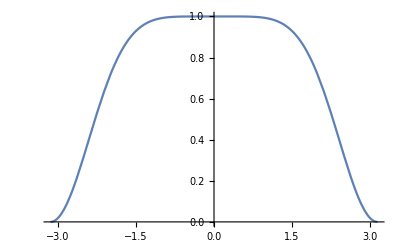

```mathematica
Series[temp3,{ϵ,0,10}]
```